(3000000000 π)/149896229

0.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {676.77}. NIntegrate obtained 2.30913 and 0.0158531 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {676.77}. NIntegrate obtained 2.30515 and 0.015509 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {676.77}. NIntegrate obtained 2.29835 and 0.0151672 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

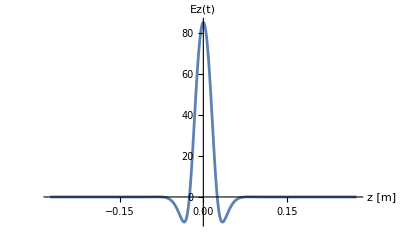
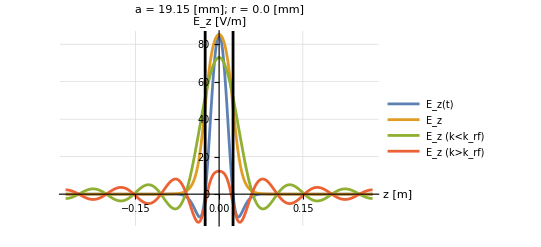

0.001915

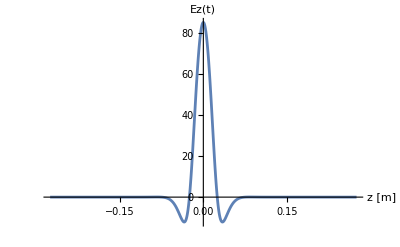
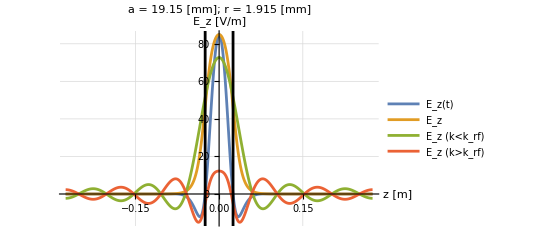

0.00383

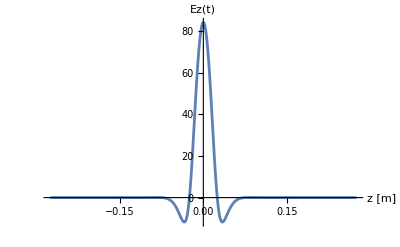
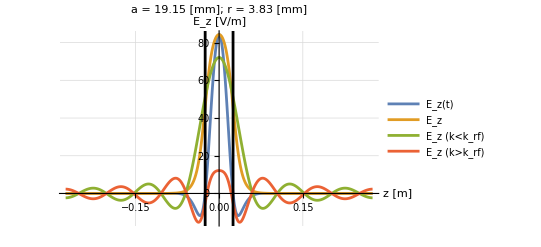

0.005745

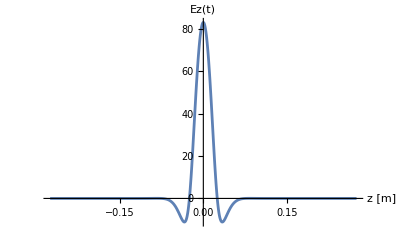
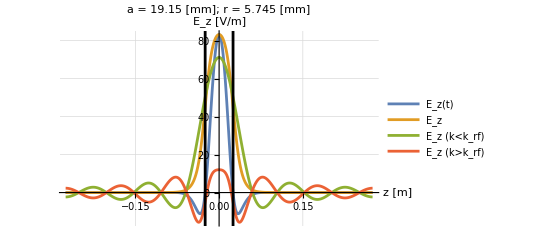

0.00766

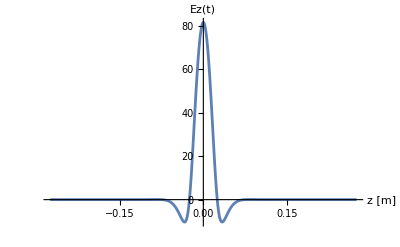
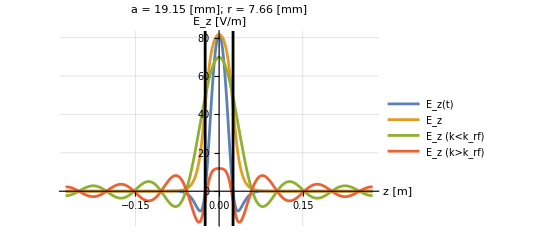

0.009575

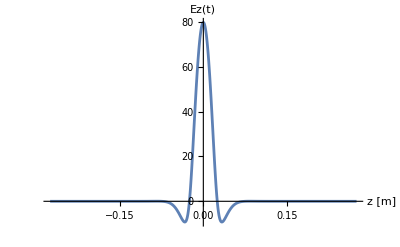
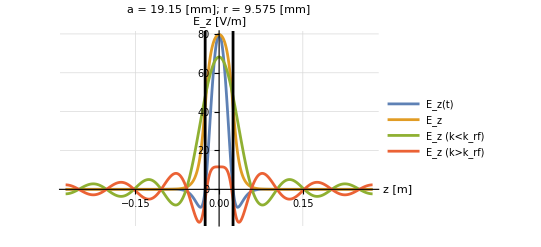

0.01149

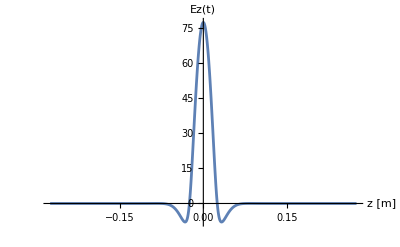
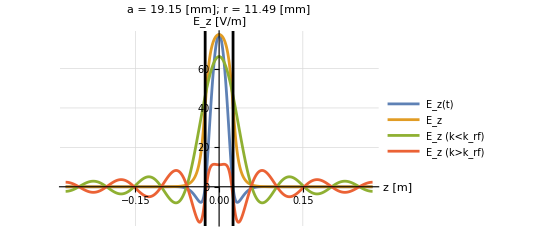

0.013405

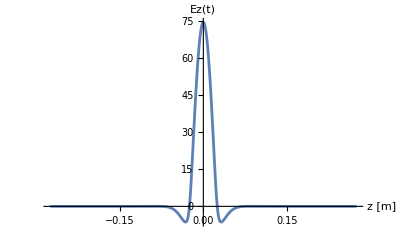
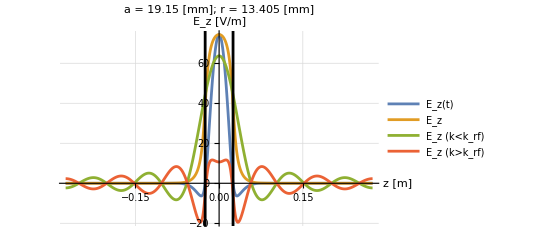

0.01532

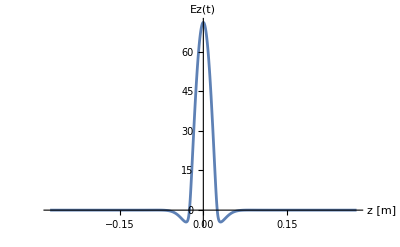
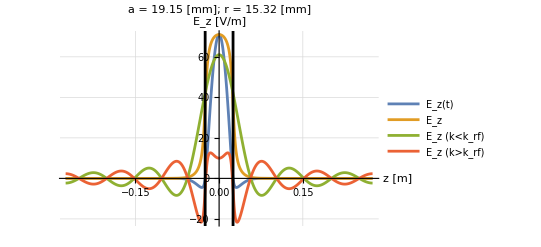

0.017235

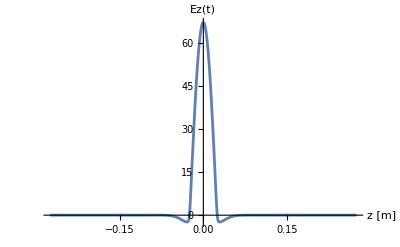
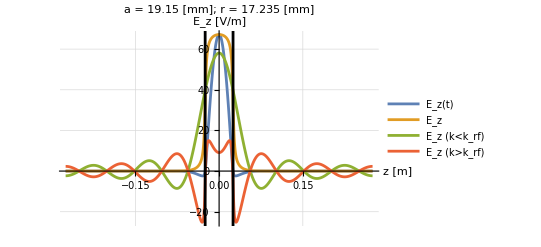

0.01915

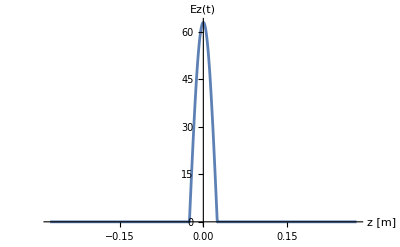
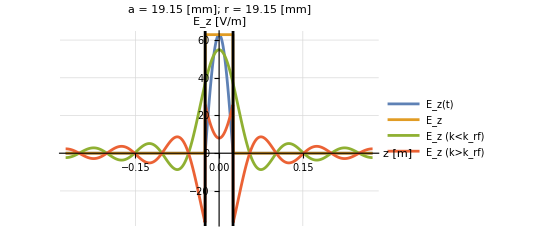

{0.,0.001915,0.00383,0.005745,0.00766,0.009575,0.01149,0.013405,0.01532,0.017235,0.01915}

{{0.,0.},{0.009575,1.},{0.01915,2.00009}}

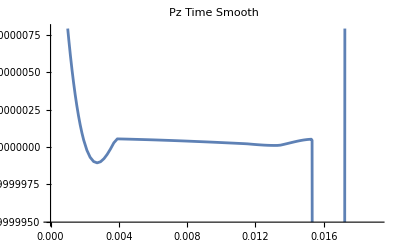

```mathematica
M = 0; (*Azimuthal order - change this to see r^m variation*)

c = 299792458; (*Speed of light*)

(*Parameters to define the cavity*)
frf = 3*10^9; (*freq [Hz]*)
Lpipe = 0.25; (*length of pipe either side [m]*)
g = c/frf/2; (*total cavity length [m]*)

aMax = 0.0383; (*total cavity radius*)
a = aMax/2; (*beam pipe radius*)

(*Parameters to define numerical steps*)
NzSteps = 1000;  (*Default = 1000*)
Noffsets = 10; (* Default = 10*)
NkSteps = 1000; (*Default = 1000*)
UpperkFactor = 5000; (*Default = 5000*)
LSpacing = 500; (*How many longitudinal points to output*)

(*derived parameters*)
kl = 2*Pi*frf/c; 
L = g/2 + Lpipe;
z = N@Subdivide[-L,L,NzSteps];

DeltaPzTime = {};

(*Determine limits for integral - do the integrals separately for J_m and I_m*)
kspecial = Pi/g/2;
klower1 = 0;
kupper1 = kl;
klower2 =kl;
kupper2 = UpperkFactor*klower2;
krange1 = N@Subdivide[klower1,kupper1,NkSteps]; (*determine the r values at which to calculate the integral*)
krange2 = N@Subdivide[klower2,kupper2,UpperkFactor*NkSteps]; (*determine the r values at which to calculate the integral*)

roffset = N@Subdivide[0,a,Noffsets]; (*determine the r values at which to calculate the integral*)

(*loop through the different radius values*)
For[i=0,i<Length[roffset],i++,

r = roffset[[i+1]];
Print[r];

(*do the integral in two parts*)
EzJ = NIntegrate[Sinc[k*g/2]*BesselJ[M,√(kl^2-k^2)*r]/BesselJ[M,√(kl^2-k^2)*a]*Cos[k*z],{k,klower1,kupper1}];
EzI = NIntegrate[Sinc[k*g/2]*BesselI[M,√(k^2-kl^2)*r]/BesselI[M,√(k^2-kl^2)*a]*Cos[k*z],{k,klower2,kupper2}];
EzT = (EzJ+EzI);

(*Collect the z and Ez data together*)
dataT=Transpose@{z,EzT};
dataJ=Transpose@{z,EzJ};
  dataI=Transpose@{z,EzI};

(*Include the klz variation*)
TimeArray = Cos[kl*z];
dataTTime = Transpose@{z,EzT*TimeArray};

(*interpolate on the uncollected values*)
funTime = Interpolation[dataTTime]; 
(*undertake the second integration*)
AppendTo[DeltaPzTime, NIntegrate[funTime[z],{z,-L,L}]];

(*Make plots to visualise*)
Plot[funTime[z],{z,-L,L},AxesLabel->{"z [m]","Ez(t)"},PlotRange->Full]
ListLinePlot[{dataTTime, dataT,dataJ,dataI},AxesLabel->{"z [m]","E_z [V/m]"}, PlotLegends ->{"E_z(t)","E_z","E_z (k<k_rf)","E_z (k>k_rf)" },GridLines->Automatic,PlotLabel-> StringTemplate["a = `1` [mm]; r = `2` [mm]"][a*1000,r*1000],PlotRange->Full,Epilog->{Directive[AbsoluteThickness[2],Black],{InfiniteLine[{g/2, g/2},{0,1}],InfiniteLine[{-g/2, -g/2},{0,1}]}}]
//Print]
Print[roffset]
Print[dataPzTime]

(*Plot the f(r) as a function of r*)
dataPzTime = Transpose@{roffset,DeltaPzTime};
funPzTime = Interpolation[dataPzTime];

Plot[funPzTime[roffset],{roffset,0,a},PlotLabel->"Pz Time Smooth"]
```